# Rocket Data Analysis

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data1 = Import["Vulcanite1.csv", "CSV"][[2;;220,1;;2]];
data2 = Import["Vulcanite2.csv", "CSV"][[2;;220,1;;2]];
data3 = Import["Vulcanite3.csv", "CSV"][[2;;180,1;;2]];
data4 = Import["Vulcanite4.csv", "CSV"][[2;;180,1;;2]];
data1[[1;;,2;;2]] = .3048*data1[[1;;,2;;2]];
data2[[1;;,2;;2]] = .3048*data2[[1;;,2;;2]];
data3[[1;;,2;;2]] = .3048*data3[[1;;,2;;2]];
data4[[1;;,2;;2]] = .3048*data4[[1;;,2;;2]];
tdata1 = Import["78G.csv","CSV"];
tdata2 = Import["G77.csv","CSV"]; 
tdata3 = Import["74W.csv","CSV"];
```

```mathematica
fig1a = ListPlot[data1];
fig2a = ListPlot[data2];
fig3a = ListPlot[data3];
fig4a = ListPlot[data4,PlotStyle->Red];
```

```mathematica
tmaxbig = 11;
tmaxsmall = 9;
tBurn1 = 1.285;
tBurn2 = 1.378;
tBurn3 = 1.04;
g = 9.8;
m1i = .123; 
m2i = .125;
m3i = .0885; 
m1f = .059; 
m2f = .059;
m3f = .043; 

slope1 = (m1i-m1f)/tBurn1;
slope2 = (m2i-m3f)/tBurn2;
slope3 = (m3i - m3f)/tBurn3;
mrocket = .6365;
```

```mathematica
m1[t_] = Piecewise[{{mrocket + m1i,t<0},{mrocket + (m1i- slope1*t),t≥0 && t<tBurn1},{mrocket + m1f,t≥tBurn1}},1];
m2[t_] =Piecewise[{{mrocket + m2i,t<0},{mrocket + (m2i- slope2*t),t≥0 && t<tBurn2},{mrocket + m2f,t≥tBurn2}},1];
m3[t_] = Piecewise[{{mrocket + m3i,t<0},{mrocket + (m3i- slope3*t),t≥0 && t<tBurn3},{mrocket + m3f,t≥tBurn3}},1];
```

```mathematica
fMotor1= Interpolation[tdata1, InterpolationOrder->1];
fMotor2 = Interpolation[tdata2, InterpolationOrder->1];
fMotor3 = Interpolation[tdata3, InterpolationOrder->1];
NIntegrate [fMotor1[t],{t,0,2}];
NIntegrate [fMotor2[t],{t,0,2}];
NIntegrate [fMotor3[t],{t,0,2}];
```

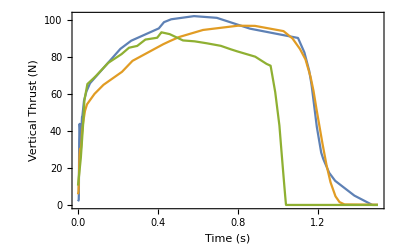

```mathematica
figt1 =Plot[{fMotor1[t],fMotor2[t],fMotor3[t]},{t,0,1.5},Frame->True,FrameLabel->{"Time (s)","Vertical Thrust (N)"}]
```

```mathematica
gr[t_] = Piecewise[{{-g,t>0}},0];
```

```mathematica
modelRocket1 = ParametricNDSolveValue[{v'[t] ==  gr[t+t0]  + (-c v[t] v[t]+fMotor1[t+t0])/m1[t+t0],
z'[t]==v[t],
v[0] ==  0,
z[0] ==  0 },z,{t,0,tmaxbig},{c,t0}];
modelRocket2 = ParametricNDSolveValue[{v'[t] ==   gr[t+t0]  + (-c v[t] v[t]+fMotor2[t+t0])/m2[t+t0],
z'[t]==v[t],
v[0] ==  0,
z[0] ==  0 },z,{t,0,tmaxbig},{c,t0}];
modelRocket3 = ParametricNDSolveValue[{v'[t] ==   gr[t+t0]  + (-c v[t] v[t]+fMotor3[t+t0])/m3[t+t0],
z'[t]==v[t],
v[0] ==  0,
z[0] ==  0 },z,{t,0,tmaxsmall},{c,t0}];
```

```mathematica
myGuess1 = {c->.001,t0 -> -.7};
myGuess2 = {c->.0009,t0 -> -.7};
myGuess3 = {c->.0015,t0 -> -.7};
myGuess4 = {c->.0013,t0 -> -.7};
```

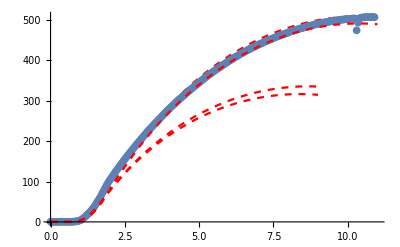

```mathematica
figGuess1 = Plot[modelRocket1[c,t0][t]/.myGuess1,{t,0,tmaxbig},PlotRange->All,PlotStyle->{Red,Dashed}];
figGuess2 = Plot[modelRocket2[c,t0][t]/.myGuess2,{t,0,tmaxbig},PlotRange->All,PlotStyle->{Red,Dashed}];
figGuess3 = Plot[modelRocket3[c,t0][t]/.myGuess3,{t,0,tmaxsmall},PlotRange->All,PlotStyle->{Red,Dashed}];
figGuess4 = Plot[modelRocket3[c,t0][t]/.myGuess4,{t,0,tmaxsmall},PlotRange->All,PlotStyle->{Red,Dashed}];
Show[figGuess1,fig1a,figGuess2,figGuess3,figGuess4]
```

```mathematica
fit1 = NonlinearModelFit[data1,modelRocket1[c,t0][t],{{t0,-.5},{c,.0009}},t];
fit2 = NonlinearModelFit[data2,modelRocket2[c,t0][t],{{t0,-.5},{c,.0008}},t];
fit3 = NonlinearModelFit[data3,modelRocket3[c,t0][t],{{t0,-.5},{c,.0013}},t];
fit4 = NonlinearModelFit[data4,modelRocket3[c,t0][t],{{t0,-.5},{c,.0011}},t];
```

```mathematica
fit1["ParameterTable"]
fit2["ParameterTable"]
fit3["ParameterTable"]
fit4["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
t0 | -0.679461 | 0.00710016 | -95.6966 | 1.93209×10^-179
c | 0.00106102 | 4.73782×10^-6 | 223.946 | 1.13621×10^-258

| Estimate | Standard Error | t-Statistic | P-Value
t0 | -0.51812 | 0.00322812 | -160.502 | 1.80455×10^-227
c | 0.000821625 | 2.0066×10^-6 | 409.462 | 2.12898941984615×10^-315

| Estimate | Standard Error | t-Statistic | P-Value
t0 | -0.693685 | 0.0066968 | -103.585 | 2.45654×10^-160
c | 0.00136979 | 8.17891×10^-6 | 167.478 | 6.94908×10^-197

| Estimate | Standard Error | t-Statistic | P-Value
t0 | -0.696672 | 0.00616399 | -113.023 | 6.11809×10^-167
c | 0.00122153 | 7.23498×10^-6 | 168.837 | 1.6778×10^-197

```mathematica
figFit1 = Plot[fit1[t],{t,0,tmaxbig},PlotStyle->{Dashed,Red}];
figFit2 = Plot[fit2[t],{t,0,tmaxbig},PlotStyle->{Dashed,Red}];
figFit3 = Plot[fit3[t],{t,0,tmaxbig},PlotStyle->{Dashed,Red}];
figFit4 = Plot[fit4[t],{t,0,tmaxbig},PlotStyle->{Dashed,Blue}];
```

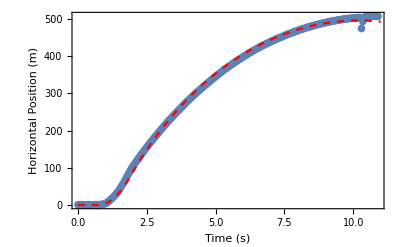

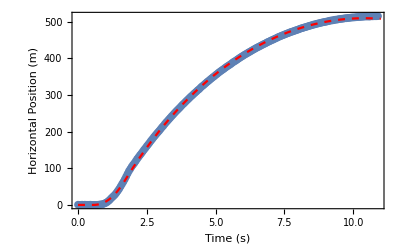

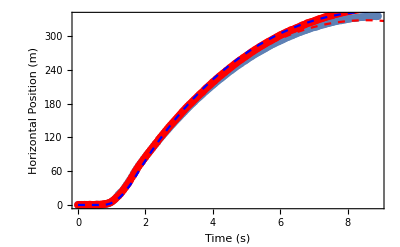

```mathematica
Show[fig1a,figFit1,Frame->True,FrameLabel->{"Time (s)","Horizontal Position (m)"}]
Show[fig2a,figFit2,Frame->True,FrameLabel->{"Time (s)","Horizontal Position (m)"}]
Show[fig3a,fig4a,figFit3,figFit4,Frame->True,FrameLabel->{"Time (s)","Horizontal Position (m)"}]
```